# Q1

{{2,(5 π)/6},{13,ArcTan[5/12]}}

{{√2,√2},{(√3)/2,3/2}}

-36+9 r^2 Cos[θ]^2+4 r^2 Sin[θ]^2

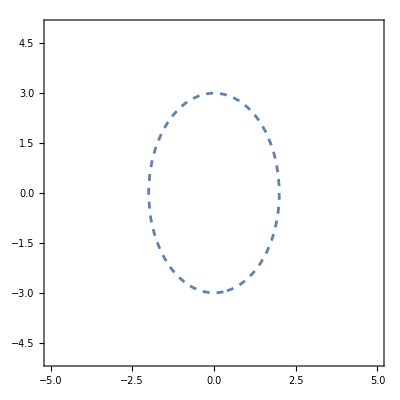

{{r→-6/(√(9 Cos[θ]^2+4 Sin[θ]^2))},{r→6/(√(9 Cos[θ]^2+4 Sin[θ]^2))}}

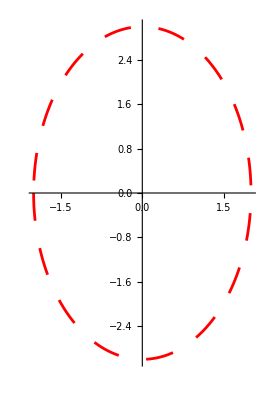

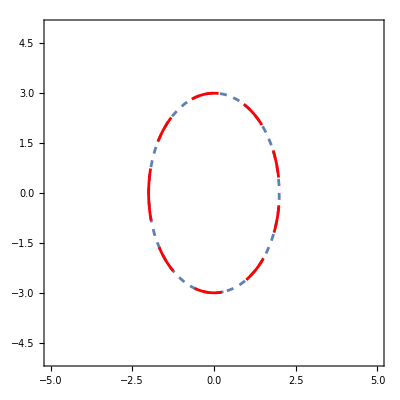

18-8 x+2 x^2+8 y+y^2

```mathematica
(*a*)
a={-Sqrt[3],1};
b={12,5};
CoordinateTransform[
"Cartesian"->"Polar",
{
a,
b
}
]
(*b*)
c={2,Pi/4};
d={Sqrt[3],Pi/3};
CoordinateTransform[
"Polar"->"Cartesian",
{
c,
d
}
]
(*c*)
f[x_,y_]:=9 x^2+4 y^2-36
f[r*Cos[θ],r*Sin[θ]]
g1=ContourPlot[
f[x,y]==0,
{x,-5,5},
{y,-5,5},
ContourStyle->{
Dashed
}
]
s = Solve[f[r*Cos[θ],r*Sin[θ]]==0,r]
g2 = PolarPlot[
s[[1,1,2]],
{θ,0,2*Pi},
PlotStyle->{
Red,
Dashed,
Dashing[0.05]
}
]
Show[g1,g2]
(*d*)
h[x_,y_]:=2*x^2+y^2-4*x+4*y
h[x-1,y+2]//Simplify
```